```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[th3]:=Subscript[θ,3];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[bev]:=Subscript[β,v];
Format[v1]:=Subscript[v,1];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];Format[si]:=σ;Format[rh]:=ρ;
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)RN={0->"s","s"+"i1"->2*"i1","s"+"y1"->"y1"+"i1","i1"->"r1","s"+"i2"->2*"i2","s"+"y2"->"y2"+"i2","i2"->"r2","r1"+"i2"->"i2"+"y2","r1"+"y2"->2*"y2","y2"->"R","r2"+"i1"->"i1"+"y1","r2"+"y1"->2*"y1","y1"->"R","r1"->"s","r2"->"s","R"->"s","s"->0,"i1"->0,"y1"->0,"r1"->0,"i2"->0,"y2"->0,"r2"->0,"R"->0};
rts={La,be1*i1*s,be1*et1*y1*s,ga1*i1,be2*i2*s,be2*et2*y2*s,ga2*i2,be2*si2*i2*r1,be2*si2*et2*y2*r1,ga2*y2,be1*si1*i1*r2,be1*si1*et1*y1*r2,ga1*y1,th1*r1,th2*r2,th3*R,mu*s,mu*i1,mu*y1,mu*r1,mu*i2,mu*y2,mu*r2,mu*R};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS,var,par, cp,mSi,Jx,Jy,E0,K,R0A,infV,gam,ngm} = bdAn[RN, rts];
Print["RHS=",RHS//FullSimplify//MatrixForm,"mSi=",mSi," K= ",K//MatrixForm,"where the order is ",infV," after permutation ",K[[{1,3,2,4},{1,3,2,4}]]//MatrixForm, "the repr. funs are",R0A];edgIGMS[RN,mSi]
```

reactions and transitions: (0→s | Λ
i1+s→2 i1 | β_1 i_1 s
s+y1→i1+y1 | β_1 η_1 s y_1
i1→r1 | γ_1 i_1
i2+s→2 i2 | β_2 i_2 s
s+y2→i2+y2 | β_2 η_2 s y_2
i2→r2 | γ_2 i_2
i2+r1→i2+y2 | β_2 i_2 r_1 σ_2
r1+y2→2 y2 | β_2 η_2 r_1 σ_2 y_2
y2→R | γ_2 y_2
i1+r2→i1+y1 | β_1 i_1 r_2 σ_1
r2+y1→2 y1 | β_1 η_1 r_2 σ_1 y_1
y1→R | γ_1 y_1
r1→s | r_1 θ_1
r2→s | r_2 θ_2
R→s | R θ_3
s→0 | μ s
i1→0 | i_1 μ
y1→0 | μ y_1
r1→0 | μ r_1
i2→0 | i_2 μ
y2→0 | μ y_2
r2→0 | μ r_2
R→0 | μ R)

RHS=(Λ+r_1 θ_1+r_2 θ_2+R θ_3-s (β_2 i_2+μ+β_1 (i_1+η_1 y_1)+β_2 η_2 y_2)
-i_1 (γ_1+μ-β_1 s)+β_1 η_1 s y_1
-((γ_1+μ) y_1)+β_1 r_2 σ_1 (i_1+η_1 y_1)
γ_1 i_1-r_1 (μ+θ_1+β_2 σ_2 (i_2+η_2 y_2))
-i_2 (γ_2+μ-β_2 s)+β_2 η_2 s y_2
-((γ_2+μ) y_2)+β_2 r_1 σ_2 (i_2+η_2 y_2)
γ_2 i_2-r_2 (μ+θ_2+β_1 σ_1 (i_1+η_1 y_1))
-R (μ+θ_3)+γ_1 y_1+γ_2 y_2)mSi={{i_1,y_1},{i_2,y_2}} K= ((β_1 s)/(γ_1+μ) | 0 | (β_1 η_1 s)/(γ_1+μ) | 0
0 | (β_2 s)/(γ_2+μ) | 0 | (β_2 η_2 s)/(γ_2+μ)
(β_1 r_2 σ_1)/(γ_1+μ) | 0 | (β_1 η_1 r_2 σ_1)/(γ_1+μ) | 0
0 | (β_2 r_1 σ_2)/(γ_2+μ) | 0 | (β_2 η_2 r_1 σ_2)/(γ_2+μ))where the order is {i_1,i_2,y_1,y_2} after permutation ((β_1 s)/(γ_1+μ) | (β_1 η_1 s)/(γ_1+μ) | 0 | 0
(β_1 r_2 σ_1)/(γ_1+μ) | (β_1 η_1 r_2 σ_1)/(γ_1+μ) | 0 | 0
0 | 0 | (β_2 s)/(γ_2+μ) | (β_2 η_2 s)/(γ_2+μ)
0 | 0 | (β_2 r_1 σ_2)/(γ_2+μ) | (β_2 η_2 r_1 σ_2)/(γ_2+μ))the repr. funs are{(β_1 (s+η_1 r_2 σ_1))/(γ_1+μ),(β_2 (s+η_2 r_1 σ_2))/(γ_2+μ)}

{}

```mathematica
bdfp=bdFp[RHS,var,mSi];
Print["rat sols on first siphon facet are"]
bd1=bdfp[[1,1]]//FullSimplify
bdfp[[1,2]]
```

fps on siphon facet {i_1,y_1}: 3 boundary points

fps on siphon facet {i_2,y_2}: 3 boundary points

rat sols on first siphon facet are

{{i_2→0,R→0,r_1→0,r_2→0,s→Λ/μ,y_2→0},{i_2→((β_2 Λ-μ (γ_2+μ)) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(β_2 γ_2 Λ-γ_2 μ (γ_2+μ))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0},{i_2→-(((μ+θ_1) (μ+θ_2) (γ_2 μ (θ_1-θ_3)+β_2 η_2 Λ σ_2 (μ+θ_3)+μ θ_1 (μ+θ_3)))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))),R→(γ_2 (μ+θ_1) (-((μ^2 (-1+σ_2)-β_2 Λ σ_2-μ θ_1) (μ+θ_2))+γ_2 μ (μ-μ σ_2+θ_1-σ_2 θ_2)))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3)))),r_1→-(((γ_2+μ) (-((μ^2 (-1+σ_2)-β_2 Λ σ_2-μ θ_1) (μ+θ_2))+γ_2 μ (μ-μ σ_2+θ_1-σ_2 θ_2)) (μ+θ_3))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))),r_2→-((γ_2 (μ+θ_1) (γ_2 μ (θ_1-θ_3)+β_2 η_2 Λ σ_2 (μ+θ_3)+μ θ_1 (μ+θ_3)))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))),s→((γ_2+μ) (μ+θ_2) (γ_2 μ (θ_1-θ_3)+β_2 η_2 Λ σ_2 (μ+θ_3)+μ θ_1 (μ+θ_3)))/(β_2 μ (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3)))),y_2→((μ+θ_1) (-((μ^2 (-1+σ_2)-β_2 Λ σ_2-μ θ_1) (μ+θ_2))+γ_2 μ (μ-μ σ_2+θ_1-σ_2 θ_2)) (μ+θ_3))/(β_2 μ σ_2 (η_2 ((μ (-1+σ_2)-θ_1) (μ+θ_2)+γ_2 (μ (-1+σ_2)-θ_1+σ_2 θ_2)) (μ+θ_3)+(μ+θ_2) (γ_2 (θ_1-θ_3)+θ_1 (μ+θ_3))))}}

AllSolsRational

```mathematica
{E1,E2,R12,R21,coP}=invN2[bdfp[[1,1]],bdfp[[2,1]],R0A,E0,par,cp,2,2];
Print["invasion numbers R12, R21 are ",R12//Apart,R21//Apart]
```

Selected sol when i1=0 is (solution 2): {i_2→((β_2 Λ-γ_2 μ-μ^2) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(γ_2 (β_2 Λ-γ_2 μ-μ^2))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0}

Selected sol when i2=0 is (solution 2): {i_1→((β_1 Λ-γ_1 μ-μ^2) (μ+θ_1))/(β_1 μ (γ_1+μ+θ_1)),R→0,r_1→(γ_1 (β_1 Λ-γ_1 μ-μ^2))/(β_1 μ (γ_1+μ+θ_1)),r_2→0,s→(γ_1+μ)/β_1,y_1→0}

under coP: {β_1→4,β_2→3,η_1→1,η_2→1,γ_1→1,γ_2→1,Λ→1,μ→1,σ_1→1,σ_2→1,θ_1→1/2,θ_2→1,θ_3→1} invasion nrs are{1.05,1.55556} repr nrs are{2.,1.5}

END invNr OUTPUT

invasion numbers R12, R21 are (β_2 (γ_1+μ))/(β_1 (γ_2+μ))+(β_1 β_2 η_2 γ_1 Λ σ_2-β_2 η_2 γ_1^2 μ σ_2-β_2 η_2 γ_1 μ^2 σ_2)/(β_1 μ (γ_2+μ) (γ_1+μ+θ_1))(β_1 (γ_2+μ))/(β_2 (γ_1+μ))+(β_1 β_2 η_1 γ_2 Λ σ_1-β_1 η_1 γ_2^2 μ σ_1-β_1 η_1 γ_2 μ^2 σ_1)/(β_2 μ (γ_1+μ) (γ_2+μ+θ_2))

```mathematica
(*E1*)
cE2=bd1[[2]]
cE1=bdfp[[2,1]][[2]]
jac=Grad[RHS,var];
j1=jac/.cE1/.{i2->0,y2->1}//FullSimplify;
cChu={et1->1,et2->1,th3->0,th1->0,th2->0,La->mu};
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]/.cChu]]//Factor
(*{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify*)
```

{i_2→((β_2 Λ-μ (γ_2+μ)) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(β_2 γ_2 Λ-γ_2 μ (γ_2+μ))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0}

{i_1→((β_1 Λ-γ_1 μ-μ^2) (μ+θ_1))/(β_1 μ (γ_1+μ+θ_1)),R→0,r_1→(γ_1 (β_1 Λ-γ_1 μ-μ^2))/(β_1 μ (γ_1+μ+θ_1)),r_2→0,s→(γ_1+μ)/β_1,y_1→0}

At cE1, chp of jac, ch1, factorizes as

Stability of E1 holds iff

β_1>0&&β_2>0&&η_1>0&&η_2>0&&γ_1>0&&γ_2>0&&Λ>0&&μ>0&&σ_1>0&&σ_2>0&&θ_1>0&&θ_2>0&&θ_3>0

Auto-determined varInd: {1,2,5}

Susceptible: s

Strain 1 (first compartment): i_1

Strain 2 (first compartment): i_2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: β_1 = 2., β_2 = 2.

Adjusted ranges: β_1 ∈ [0.001, 8.], β_2 ∈ [0.001, 6.]

Scanning 2500 parameter combinations...

Checked 730 potential coexistence points

All Rij equations: {β_1/2==1,β_2/2==1,((3+β_1) β_2)/(5 β_1)==1,(β_1 (4+β_2))/(6 β_2)==1}

DFE: 221 (9%)

E2: 612 (24%)

E1: 937 (37%)

EE-Stable: 713 (29%)

NoSol: 17 (1%)

{7.26563,Null}

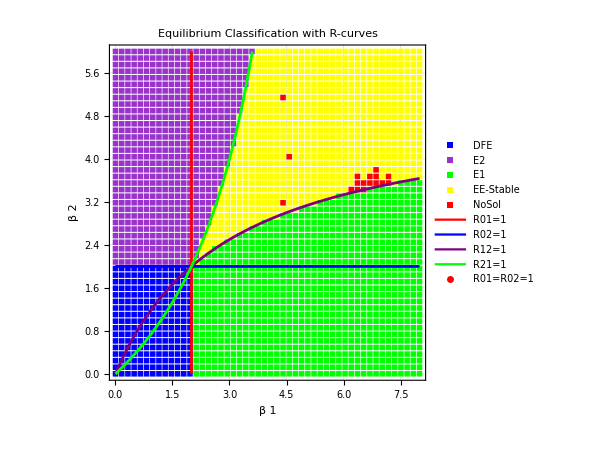

```mathematica
{R01,R02}=R0A/.E0;gridRes=50;plotInd={1,2};steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[(*Step 3:Scanning-now with mSi from step 1*)
{plot,noSol,results}=scan[RHS,var,par,coP,plotInd,mSi,(*mSi auto-provided*)gridRes,steTol,staTol,choTol,R01,R02,R12,R21];]
plot
```

```mathematica
Export["GavScan.pdf",plot]
```

GavScan.pdf